# Homework 10

## Exercise 1

Theorem 12.2: Suppose the sequence {x_n} has a limit x.  That means that if we go far enough out into the sequence (i.e. n > N_x), we can get arbitrariliy close to x.  That is, |x_(n > N_x) - x| < ϵ/2.  Similarly, for the sequence {y_n}, we can also get arbitrarily close to its limit y by going far enough out into the series (i.e ∀_(n>N_y) |y_n- y| < ϵ/2).  We choose the larger of N_x and N_y and call this N.  Then 

∀_(n > N) |x_n - x| < ϵ/2 ∧ |y_n - y| < ϵ/2
We add the n^th terms of the two sequence (where n > N) and subtract sum of their limits:
|{x_n} + {y_n} - (x + y)| = |x_n - x + y_n - y|.  We know from previously that the first difference is < ϵ/2 and the second difference is also < ϵ/2.
Therefore:
|x_n - x + y_n - y| < |ϵ/2 + ϵ/2| = ϵ

Theorem 12.3: 12.2  By adding and subtracting x y_n and y y_n and rearraning terms we can obtain that 
|x (y - y_n| + (x - x_n)| |y_n y| + (x - x_n)y|. 
By the properties of the distance metric (i.e. ||) we know the above is less than
≤ |x| | y - y_n| + |x x_n| |y_n y| + |x - x_n| |y|.  We pick an N large enough such that the terms with the factor x_n and y_n tend to be arbitrarily close to zero  This can be done by picking ϵ such that
|x - x_n| <ϵ/(3(|y| + 1))
|y - y_n| <ϵ/(3(|x| + 1))

Substituting above, leads to lim_(n→∞)  {x_n y_n} = xy.

Theorem 12.4 Choose a positive ϵ such that it is less than xb.  Then it must be the case that b < x ϵ.  Construct an interval of width ϵ around x: (x - ϵ, x + ϵ), which will be to the right of b on the number line.  For a large enough n, all x_n are inside this interval (that is b < x_n).  This is a contradiction of x_n < b.

## Exercise 2

## Exercise 3

Let g(x) = f(x) - x.  Suppose g(a) ≥ 0 ∧ g(b) ≤ 0.  That is: g(a) - a ≥ 0 ∧ g(b) - b ≤ 0.  Since g is continuous, ∃_c g(c) - c = 0. Therefore, there must be a c such that g(c) = c.  so there must be a fixed point.

Intuitively, by f being continuous, we guarantee that f approaches x smoothly (that is, we can apply the intermediate value theorem).

## Exercise 4

Suppose that {s_n} is a bounded, increasing monotone sequence. Let u be the supremum of {s_n} and let ϵ be a positive number. Then ∃_(N ∈ ℕ^+) u - ϵ < s_N ≤ u. Since {s_n} is increasing, u − ϵ <s_n ≤ u for all n>N. Therefore, |u − s_n| < ϵ for all n>N and s_n → u. (http://math.uh.edu/~almus/4389_AN_ch2.pdf)

Similarly if {s_n} is bounded decreasing monotone, there exists a lower limit.

## Exercise 5

If a series converges then:
lim_(n → ∞)  ∑_(k = 1)^n a_k = L.
This can be rewritten as:
lim_(n → ∞)  a_n + lim_(n → ∞)  ∑_(k = 1)^(n-1) a_k
The second limit also tends to L thus the above can be rewritten as:
lim_(n → ∞)  a_n + L
If this limit is to equal L, then lim_(n → ∞)  a_n must equal 0.
(http://math.stackexchange.com/questions/107961/if-a-series-converges-then-the-sequence-of-terms-converges-to-0)

## Exercise 6

Consider the series associated with the geometric distribution
a_k = P(K=k) =p(1-p)^k, 0 < p < 1
We find the limit of the sequence as k → ∞
lim_(k → ∞) a_k = lim_(k → ∞) p(1-p)^k
Since p is a constant, we can rewrite as:
 lim_(k → ∞) p(1-p)^k = p lim_(k → ∞)  (1-p)^k = 0 (because |1-p| < 1

## Exercise 7

Consider the geometric series ∑_(k = 0)^∞ x^k, |x| < 1
This series converges to:
∑_(k = 0)^∞ x^k = 1/(1-x)
Differentiating (term by term), we obtain:
ⅆ/ⅆx∑_(k = 0)^∞ x^k = (ⅆ 1/(1-x))/ⅆx
∑_(k = 0)^∞ k x^(k-1) = 1/(1-x)^2
Multiplying by x:
∑_(k = 0)^∞ k x^k = x/(1-x)^2
Now consider the geometric series given by
Pr(X=k) = p(1-p)^k
The expected value is:
∑_(k = 1)^∞  k (1-p)^kp = (p(1-p))/(1-(1-p))^2= (p(1-p))/p^2 = (1-p)/p

## Exercise 8

Q_t^d = d_0 - d_1 P_t
Q_t^s = s_0 - s_1 P_(t-1)

In equilbrium, supply equals demand:
d_0 - d_1 P_t = s_0 - s_1 P_(t-1)
P_t = (s_0-d_0 - s_1 P_(t-1))/-d_1
or
P_t = (d_0 - s_0)/d_1 - s_1/d_1 P_(t-1)
P_ss = 1/(1+s_1/d_1) (d_0- s_0)/d_1
Simplifying:
P_ss = (d_0-s_0)/(d_1+s_1)
The economic interpretation of the condition that P_ss > 0 iff d_0 > s_0 is that there must consumer surplus (at 1 unit of production) must be strictly greater than the fixed cost of production for the market to exist.

## Exercise 9

Any fixed point on a contracting mapping must be unique, because if there are two unique fixed points, the distance between these points will be the same in the image as in the preimage.  However, for a contraction mapping, two points in the image must be closer than they are in the preimage.

Construct the series (x_t) by function iteration: (x_t) = f^(○t)(x). Because f is a contraction mapping:
d(f(x_t), f(x)) ≤ λd(x_t, x), λ ∈ [0, 1)

or
d(x_(t+1), x) ≤ λd(x_t, x) ≤ λ^(t+1)d(x_0, x)
which tends to 0 because λ^(t+1) tends to 0.  Thus d(x_t, x) ≤ 0.  Since distance must be positive: lim_(t→∞)  d(x_t, x) = 0.

## Exercise 10

A contraction mapping is a mapping from a set to itself such that the distance between two points is always greater than the distance between their images.

f(x) = x/2, x ∈ ℝ is a contraction mapping because the distance between two points in the image is always 1/2 the distance between them in the preimage.  By Banach’s theorem, there is a unique fixed point.
f(X) = 1/x, 0 < x< 1 is not a contraction mapping because the distance between two points in the image is always greater than the distance between them in the preimage.
f(x) = 1/(1+x) 0 < x < 1.  Note that if x > 0 then 1/(1+x).  Thus the distance between two points in the image is always less than the distance between two points in the preimage:
||(f(x_0) - f(x_1)||  = 1/(1+x_0) - 1/(1 + x_1) = (1+x_1 + 1 + x_0)/((1+x_0) (1 + x_1)) = (x_1 - x_0)/(1 + x_1+ x_0 + x_0 x_1) . Since 0 < x_0  < 1 and 0 < x_1 < 1, (x_0 x_1) << 1 (i.e. very small). Ignoring this term, we have:
 (x_1- x_0)/(1 + x_1+ x_0) which must be < ||x_1 - x_0||
 By Banach’s theorem, there is a unique fixed point.

## Exercise 11

Consider the present value of the cash stream if the buyout is accepted:
15000 - 200 ((1- (1.01)^-60)/(.01)) = 15000 - 8991.01 = 6009.00
Consider the present value of the alternative:
200 ((1- (1.01)^-60)/(.01)) = 8991.01
Not accepting the buyout offer is better.

```mathematica
15000 - TimeValue[Annuity[200,60], .01, 0]
```

6008.99

## Computational Exercise 1

The effective annual yield is the rate that equates the return based on a nominal rate that is compounded at a frequency other than annually with the return with annual compounding.

For example, if a nominal rate is 10% a year compounded monthly, the effective annual rate is 10.47%.

```mathematica
pv1eay[i0_, t0_] := Module[{i=i0,t=t0},(1+i/100)^t]
```

```mathematica
pv1eay[10, 1]
```

11/10

```mathematica
pvstream[lst_, i_, pv1fn_] := Module[{list = lst, rate = i, f = pv1fn}, Do[Print[N[f[rate, time]*list[[time]]]],{time,Length[list]}]]
```

```mathematica
pvstream[Table[1000, 10], 5, pv1eay]
```

1050.

1102.5

1157.63

1215.51

1276.28

1340.1

1407.1

1477.46

1551.33

1628.89

```mathematica
pv1cont[i0_, t0_] := Module[{i=i0,t=t0},Exp[i/100*t]]
```

```mathematica
pv1cont[5, 10]
```

√ⅇ

```mathematica
pvstream[Table[1000, 10], 5, pv1cont]
```

1051.27

1105.17

1161.83

1221.4

1284.03

1349.86

1419.07

1491.82

1568.31

1648.72

```mathematica
payments = FoldList[#1+50&, Table[1000, 10]]
```

{1000,1050,1100,1150,1200,1250,1300,1350,1400,1450}

```mathematica
pvstream[payments, 5, pv1eay]
```

1050.

1157.63

1273.39

1397.83

1531.54

1675.12

1829.23

1994.56

2171.86

2361.9

```mathematica
pvstream[payments, 5, pv1cont]
```

1051.27

1160.43

1278.02

1404.61

1540.83

1687.32

1844.79

2013.96

2195.64

2390.65

## Computational Exercise 2

```mathematica
Solve[5000(1+r)^2 == 5408 && r ≥ 0]
```

{{r→1/25}}

```mathematica
10000.*(1+1/25)^3
```

11248.6

## Computational Exercise 3

```mathematica
picard[fn_, p0_, eps_,t_] := Module[{limit = t, f = fn, p=p0, e = eps, times = 0},
result = {};
While[True,(
times = times + 1;
If[times ≥ limit, Return[result]];
p1 =p;
 p=f[p];
If[Abs[p1 - p] < e, Return[result], AppendTo[result, p]];
)]] ;
```

```mathematica
fp1 = picard[x ↦(x+2.0)/x, 1, 1E-6, 100]
```

{3.,1.66667,2.2,1.90909,2.04762,1.97674,2.01176,1.99415,2.00293,1.99854,2.00073,1.99963,2.00018,1.99991,2.00005,1.99998,2.00001,1.99999,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}

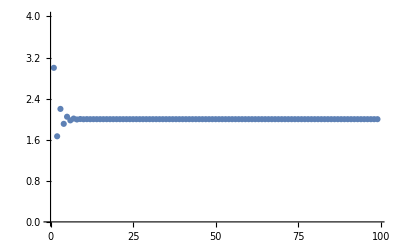

```mathematica
ListPlot[fp1]
```

```mathematica
fp2 = picard[x ↦(x+1.0)/x, 1, 1E-6, 100]
```

{2.,1.5,1.66667,1.6,1.625,1.61538,1.61905,1.61765,1.61818,1.61798,1.61806,1.61803,1.61804,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

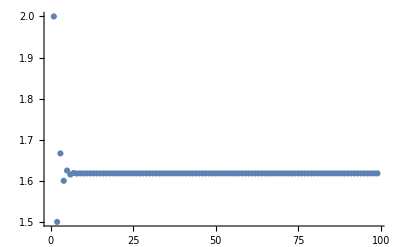

```mathematica
ListPlot[fp2]
```

## Computational Exercise 4

When markets clear we have Q_d = Q_s.  That is:
500 - 2 P_t = 50 + P_(t-1)
P_t = (-P_(t-1))/2 + 225

```mathematica
FullSimplify[Solve[500-2pt == 50+pt1, pt]]
```

{{pt→225-pt1/2}}

```mathematica
fp3 = picard[ p ↦ -0.5p+225, 1, 1E-3, 100]
```

{224.5,112.75,168.625,140.688,154.656,147.672,151.164,149.418,150.291,149.854,150.073,149.964,150.018,149.991,150.005,149.998,150.001,149.999,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.,150.}

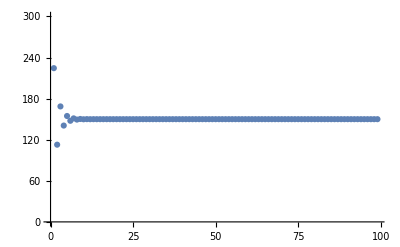

```mathematica
ListPlot[fp3]
```

There is a steady state. The price convereges to ~$150.

```mathematica
FullSimplify[Solve[500-2pt == 50+3pt1, pt]]
```

{{pt→225-(3 pt1)/2}}

```mathematica
fp4 =picard[p↦225-(3.*p/2), 1, 1E-3, 10]
```

{223.5,-110.25,390.375,-360.563,765.844,-923.766,1610.65,-2190.97,3511.46}

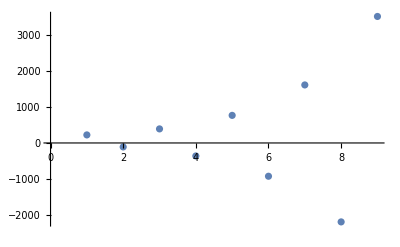

```mathematica
ListPlot[fp4]
```

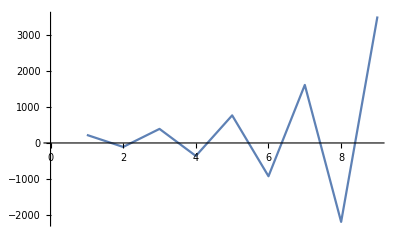

```mathematica
ListLinePlot[fp4]
```

```mathematica
GeometricDistribution[0.10]
```

GeometricDistribution[0.1]

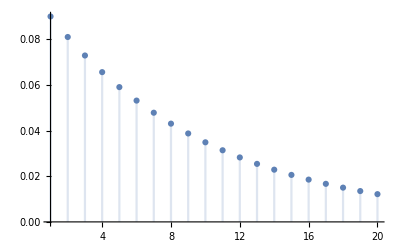

```mathematica
DiscretePlot[PDF[GeometricDistribution[0.1], x], {x, 20}]
```

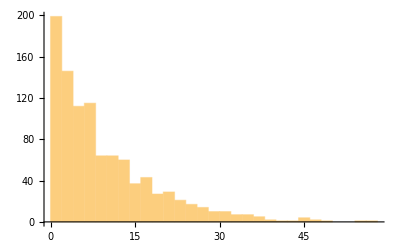

```mathematica
Histogram[RandomVariate[GeometricDistribution[0.1],1000]]
```